## Extracting info from 1904.07265

### Data

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Transformation function

```mathematica
Clear[f]
f[Ere_,Etrue_]:=(*1/σe*)Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}]
```

```mathematica
dataN=Table[Maximize[f[i*.5,x],x][[2,1,2]],{i,40}]
```

{1.11111,2.22222,3.33333,4.44444,5.55556,6.66667,7.77778,8.88889,10.,11.1111,12.2222,13.3333,14.4444,15.5556,16.6667,17.7778,18.8889,20.,21.1111,22.2222,23.3333,24.4444,25.5556,26.6667,27.7778,28.8889,30.,31.1111,32.2222,33.3333,34.4444,35.5556,36.6667,37.7778,38.8889,40.,41.1111,42.2222,43.3333,44.4444}

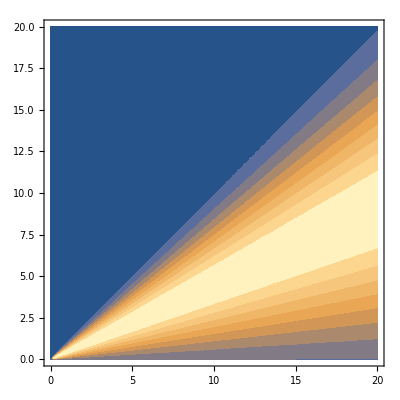

```mathematica
ContourPlot[f[ere,etrue],{etrue,0,20},{ere,0,20},ContourLines->False]//Quiet
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

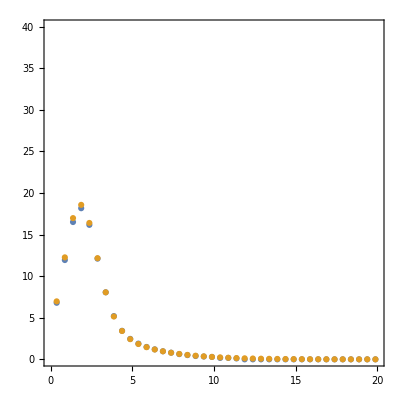

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

### Introducing NSI

```mathematica
(* choosing Subscript[ϵ, μτ] only real *)
```

```mathematica
ratio[epS_,ee_]=(1.3108065554447088 (-0.0030877550532743044-0.009954498061660128 ee+0.23176694498280875 ee^2-0.1967477254913792 epS-0.31714381779784007 ee epS+15.391226954752788 ee^2 epS-3.1341271261934094 epS^2+(0.+4.8135532529529774*^-15 ⅈ) ee epS^2+255.4726050250257 ee^2 epS^2+(-29.535775009807654 (-0.003245843462319231+1. ee^2) epS+ee epS (-0.5449208925062372+34.12233216000002 ee epS)+0.49323021260695565 (0.02018225527800879 ee-0.1669834711689695 epS+50.18153472 ee^2 epS)+0.3387236974426105 (-0.0061845730062581265+4.508553721562175 epS^2-(0.+1.4210854715202002*^-14 ⅈ) ee epS^2+ee^2 (1.9053823999999995-1389.0237696 epS^2))+0.5819997400709132 (0.0061845730062581265+ee (0.5449208925062372+(0.+1.4210854715202002*^-14 ⅈ) epS) epS-4.508553721562175 epS^2+ee^2 (-1.9053823999999995+1354.9014374399997 epS^2))) Cos[8.323065282815573/ee]+(-10.606500983834069 (0.036484675267957206+1. ee^2) epS+(25.339040586664918+694.5118848 ee^2) epS^2+0.5819997400709132 (0.03475862906264049-50.678081173329836 epS^2+ee^2 (0.9526911999999997-1389.0237696 epS^2))+0.3387236974426105 (-0.03475862906264049+25.339040586664918 epS^2+ee^2 (-0.9526911999999997+694.5118848 epS^2))) Cos[8.323065282815573/ee]^2+ee (epS (-0.729457332827302+8.555102338081564 epS)+0.3387236974426105 (0.30018944920750323-2.917829331309208 epS-218.83810847226988 epS^2)+0.49323021260695565 (0.027016938252863044+7.788259486451421 epS-39.39069597267431 epS^2)+0.2870598555323694 (-0.05403387650572609-16.210230257205176 epS+39.39069597267431 epS^2)+0.5819997400709132 (-0.30018944920750323+3.647286664136511 epS+210.28300613418835 epS^2)) Sin[8.323065282815573/ee]+(-10.606500983834069 (0.036484675267957206+1. ee^2) epS+(25.339040586664918+694.5118848 ee^2) epS^2+0.5819997400709132 (0.03475862906264049-50.678081173329836 epS^2+ee^2 (0.9526911999999997-1389.0237696 epS^2))+0.3387236974426105 (-0.03475862906264049+25.339040586664918 epS^2+ee^2 (-0.9526911999999997+694.5118848 epS^2))) Sin[8.323065282815573/ee]^2))/(-0.004047449565439481-0.013048421315385748 ee+0.303801630818859 ee^2+(0.013048421315385748 ee+0.7628890745520696 (0.006184573006258115-1.9053824000000001 ee^2)+0.444001243092244 (-0.006184573006258115+1.9053824000000001 ee^2)) Cos[8.323065282815573/ee]+0.7628890745520696 (0.034758629062640496+0.9526912000000001 ee^2+0.5819997400709132 (-0.034758629062640496-0.9526912000000001 ee^2)) Cos[8.323065282815573/ee]^2-0.09859138154688124 ee Sin[8.323065282815573/ee]+0.7628890745520696 (0.034758629062640496+0.9526912000000001 ee^2+0.5819997400709132 (-0.034758629062640496-0.9526912000000001 ee^2)) Sin[8.323065282815573/ee]^2);
```

### Plot NSI

```mathematica
(*limite on Subscript[ϵ̃, 23] : 0.08 from my paper with JS *)
(* Subscript[ϵ̃, 23] = Subscript[p, μ] Subscript[ϵ, 23] = 27 Subscript[ϵ, 23] *)
```

```mathematica
Solve[0.08==x*27,x]
```

{{x→0.00296296}}

```mathematica
nsi=0.003;
nsi2=nsi*10;
nsi3=nsi*100;
```

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

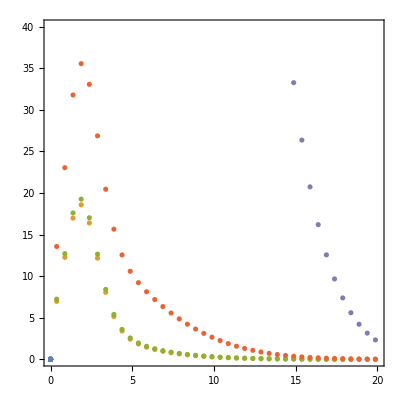

```mathematica
dataNSI=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratio[nsi,.5*i],{i,40}]},{j,40}]//Quiet;
dataNSI2=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratio[nsi2,.5*i],{i,40}]},{j,40}]//Quiet;
dataNSI3=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratio[nsi3,.5*i],{i,40}]},{j,40}]//Quiet;
ListPlot[{data*0,dataT,dataNSI,dataNSI2,dataNSI3},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

```mathematica
Transpose[{dataT[[All,2]],dataNSI[[All,2]]}]//Chop
```

{{6.97108,7.23176},{12.2612,12.7115},{16.9807,17.6031},{18.5749,19.2634},{16.398,17.0225},{12.1658,12.6522},{8.06067,8.40904},{5.15012,5.39813},{3.41041,3.59627},{2.42756,2.57617},{1.84576,1.97026},{1.46299,1.5698},{1.18441,1.2769},{0.968088,1.04829},{0.794312,0.863747},{0.65239,0.712294},{0.535537,0.586994},{0.438937,0.482925},{0.358948,0.396352},{0.292705,0.324335},{0.237899,0.264493},{0.192641,0.214868},{0.155364,0.173828},{0.124757,0.14},{0.0997192,0.112224},{0.0793215,0.089514},{0.0627787,0.0710326},{0.0494268,0.0560671},{0.0387054,0.0440122},{0.0301422,0.034355},{0.0233408,0.0266625},{0.0179696,0.020571},{0.0137529,0.0157762},{0.0104624,0.0120252},{0.00791051,0.00910923},{0.00594381,0.00685678},{0.00443777,0.00512816},{0.00329194,0.00381026},{0.00242592,0.00281221},{0.00177576,0.00206153}}

```mathematica
(* checking if it is needed to integrate probability over bin *)
```

```mathematica
Table[{NIntegrate[ratio[nsi,ee]/.5,{ee,.5*(i-1),.5*i}],ratio[nsi,.5*i]//Chop,ratio[nsi,.5*i]/NIntegrate[ratio[nsi,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
Table[{NIntegrate[ratio[nsi2,ee]/.5,{ee,.5*(i-1),.5*i}],ratio[nsi2,.5*i]//Chop,ratio[nsi2,.5*i]/NIntegrate[ratio[nsi2,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
Table[{NIntegrate[ratio[nsi3,ee]/.5,{ee,.5*(i-1),.5*i}],ratio[nsi3,.5*i]//Chop,ratio[nsi3,.5*i]/NIntegrate[ratio[nsi3,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
```

{{0.757229,1.0207,1.34794},{1.02806,1.03305,1.00486},{1.59332,1.05223,0.660403},{1.03634,1.0317,0.995526},{1.03112,1.03096,0.999839},{1.03119,1.03154,1.00033},{1.03204,1.0326,1.00055},{1.03327,1.03399,1.00069},{1.03479,1.03564,1.00082},{1.03656,1.03753,1.00093},{1.03857,1.03966,1.00104},{1.04081,1.04201,1.00115},{1.04327,1.04458,1.00125},{1.04595,1.04737,1.00135},{1.04885,1.05038,1.00145},{1.05197,1.0536,1.00155},{1.0553,1.05704,1.00165},{1.05885,1.0607,1.00174},{1.06261,1.06457,1.00184},{1.06659,1.06865,1.00193},{1.07078,1.07295,1.00202},{1.07518,1.07746,1.00211},{1.0798,1.08218,1.0022},{1.08463,1.08712,1.00229},{1.08968,1.09227,1.00238},{1.09494,1.09764,1.00247},{1.10041,1.10321,1.00255},{1.10609,1.109,1.00263},{1.11199,1.11501,1.00272},{1.1181,1.12122,1.0028},{1.12442,1.12765,1.00287},{1.13096,1.1343,1.00295},{1.13771,1.14115,1.00303},{1.14467,1.14822,1.0031},{1.15184,1.1555,1.00318},{1.15923,1.16299,1.00325},{1.16683,1.1707,1.00332},{1.17464,1.17862,1.00339},{1.18266,1.18675,1.00345},{1.1909,1.19509,1.00352}}

{{4.6379,1.30076,0.280463},{11.5155,1.68761,0.146551},{84.5647,4.75984,0.0562863},{2.26469,1.50763,0.66571},{1.38819,1.33393,0.96091},{1.34156,1.3652,1.01762},{1.41044,1.46349,1.03762},{1.52931,1.60057,1.0466},{1.68166,1.76727,1.05091},{1.86147,1.95978,1.05281},{2.06607,2.17626,1.05333},{2.29412,2.41574,1.05302},{2.54484,2.67764,1.05218},{2.8178,2.96161,1.05104},{3.1127,3.26742,1.04971},{3.42936,3.59491,1.04827},{3.76766,3.94399,1.0468},{4.1275,4.31458,1.04533},{4.50881,4.70662,1.04387},{4.91156,5.12007,1.04245},{5.33571,5.55491,1.04108},{5.78122,6.0111,1.03976},{6.24808,6.48863,1.0385},{6.73628,6.98748,1.03729},{7.24579,7.50765,1.03614},{7.77661,8.04912,1.03504},{8.32873,8.61189,1.034},{8.90214,9.19595,1.033},{9.49684,9.80129,1.03206},{10.1128,10.4279,1.03116},{10.7501,11.0758,1.0303},{11.4086,11.745,1.02948},{12.0884,12.4354,1.0287},{12.7895,13.1471,1.02796},{13.5119,13.8801,1.02725},{14.2555,14.6344,1.02658},{15.0203,15.4099,1.02593},{15.8065,16.2066,1.02532},{16.6139,17.0247,1.02473},{17.4425,17.864,1.02416}}

{{646.443,13.3823,0.0207015},{1129.65,43.5832,0.0385812},{8599.8,362.348,0.0421345},{103.778,25.138,0.242229},{12.5768,6.77373,0.538589},{7.37871,9.63492,1.30577},{14.1096,19.3824,1.37371},{25.9538,33.0766,1.27444},{41.1914,49.7627,1.20808},{59.1974,69.0453,1.16636},{79.6943,90.7339,1.13853},{102.541,114.726,1.11883},{127.66,140.964,1.10421},{155.004,169.409,1.09294},{184.543,200.04,1.08397},{216.26,232.84,1.07667},{250.14,267.799,1.0706},{286.174,304.908,1.06546},{324.357,344.163,1.06106},{364.683,385.559,1.05725},{407.148,429.093,1.0539},{451.75,474.763,1.05094},{498.487,522.567,1.04831},{547.357,572.503,1.04594},{598.359,624.57,1.04381},{651.491,678.767,1.04187},{706.753,735.094,1.0401},{764.144,793.55,1.03848},{823.664,854.134,1.03699},{885.312,916.846,1.03562},{949.088,981.685,1.03435},{1014.99,1048.65,1.03316},{1083.02,1117.75,1.03206},{1153.18,1188.97,1.03103},{1225.46,1262.31,1.03007},{1299.87,1337.79,1.02917},{1376.41,1415.39,1.02832},{1455.07,1495.11,1.02752},{1535.86,1576.97,1.02676},{1618.78,1660.94,1.02605}}

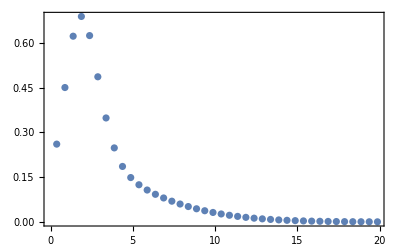

```mathematica
ListPlot[Transpose@{dataT[[All,1]],-dataT[[All,2]]+dataNSI[[All,2]]},Frame->True]
```

```mathematica
Manipulate[Plot[ratio[eps,ee],{ee,.5,20},Frame->True],{eps,0,10^-1}]
```

### Checks

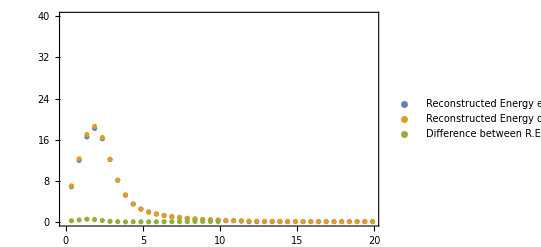

```mathematica
ListPlot[{data,dataT,Transpose[{data[[1;;20,1]],(dataT[[1;;20,2]]-data[[1;;20,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy extracted from figure","Reconstructed Energy obtained internally","Difference between R.E. obtained internally and extracted from figure"},PlotRange->{All,range}]
```

The NSI modulus is 0.003

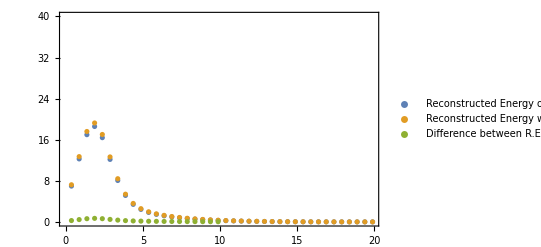

```mathematica
Print["The NSI modulus is ",nsi];ListPlot[{dataT,dataNSI,Transpose[{dataT[[1;;20,1]],(-dataT[[1;;20,2]]+dataNSI[[1;;20,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy obtained internally","Reconstructed Energy with NSI","Difference between R.E. with NSI and obtained internally"},PlotRange->{All,range}]
```

The NSI modulus is 0.03

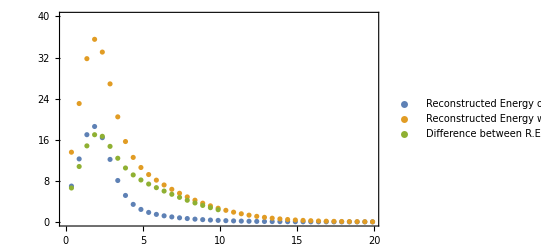

```mathematica
Print["The NSI modulus is ",nsi2];ListPlot[{dataT,dataNSI2,Transpose[{dataT[[1;;20,1]],(-dataT[[1;;20,2]]+dataNSI2[[1;;20,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy obtained internally","Reconstructed Energy with NSI","Difference between R.E. with NSI and obtained internally"},PlotRange->{All,range}]
```

The NSI modulus is 0.3

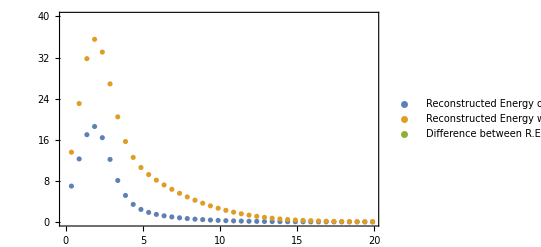

```mathematica
Print["The NSI modulus is ",nsi3];ListPlot[{dataT,dataNSI2,Transpose[{dataT[[1;;20,1]],(-dataT[[1;;20,2]]+dataNSI3[[1;;20,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy obtained internally","Reconstructed Energy with NSI","Difference between R.E. with NSI and obtained internally"},PlotRange->{All,range}]
```